# Experiment 9 - Ph6

In this experiment, we use a mass spectrometer to check the validity of the Lorentz force law for the dynamics of certain ions as described in the notes. We then determine a value for e/m_AMU, the ratio of the electron charge to the atomic mass unit.

We will do all calculations using the mass of a neutral atom of each isotope in place of the mass of the corresponding ion. Observe that the mass of an electron is approximately 0.000549 amu, such that our assumption induces an error of 0.0024% in the mass of the Sodium-23 ion that we use for our calculations. This is the lightest element we will be working with, and for heavier elements the error is even smaller. This assumption is therefore not a significant source of error, particularly given the 0.10 - 0.23% error induced in the mass term by the m = W × m_AMU assumption, where W is the (integer) atomic weight.

```mathematica
(* We import data for the B and V values at the peak for each isotope. *)
SetDirectory[NotebookDirectory[]];
data=Import["raw_data.csv","CSV"];
data//TableForm
```

Isotope |  B |  V
Cesium133 | 0.5298 | 546.7
Cesium133 | 0.5209 | 527.4
Cesium133 | 0.5405 | 569.4
Rubidium85 | 0.4239 | 549.2
Rubidium85 | 0.413 | 521.3
Rubidium85 | 0.4161 | 529.5
Rubidium87 | 0.4239 | 536.15
Rubidium87 | 0.4321 | 557.2
Rubidium87 | 0.4283 | 548.8
Rubidium87 | 0.4384 | 573.3
Potassium39 | 0.2874 | 549.4
Potassium39 | 0.297 | 587.2
Potassium39 | 0.2913 | 565.5
Potassium41 | 0.2873 | 520.6
Potassium41 | 0.2962 | 556.2
Potassium41 | 0.2913 | 531.
Sodium23 | 0.2196 | 542.9
Sodium23 | 0.2217 | 553.8
Sodium23 | 0.216 | 525.4
Chlorine35 | 0.2718 | 562.9
Chlorine35 | 0.2807 | 595.8
Chlorine35 | 0.2625 | 520.3
Chlorine37 | 0.2718 | 531.
Chlorine37 | 0.2807 | 565.2
Chlorine37 | 0.2648 | 501.5

```mathematica
(* We transform the raw data into W and B^2/V pairs to prime it for analysis with CurveFit. *)
```

```mathematica
processed=Join[{{"S","W","(B^2)/V"},{"S"}},
Table[{IsotopeData[data[[i]][[1]],"MassNumber"],(data[[i]][[2]])^2/(data[[i]][[3]])},{i,2,Length[data]}]];
Export["data.dat",processed];
```

```mathematica
(* We now use CurveFit for the rest of the analysis *)
```

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 4/data.dat

File comment header:

W	(B^2)/V

LoadFile::sorted: Data sorted in increasing x order.

Read 25 data points.

```mathematica
(* We use CurveFit to use (B,V) pairs corresponding to the same isotope to estimate the uncertainty in B^2/V. *)
```

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
LinearFit[]
```

n = 25

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-1.74672×10^-6 | b= 
3.87237×10^-6 | 
σ_a= 
5.69852×10^-7 | σ_b= 
8.09107×10^-9 | Std. deviation= 
1.41832×10^-6

Fit of (x,y±σ_y)

a= 
3.22344×10^-7 | b= 
3.84468×10^-6 | 
σ_a= 
3.79739×10^-8 | σ_b= 
1.0721×10^-9 | χ^2/(n-2)= 
15.1099

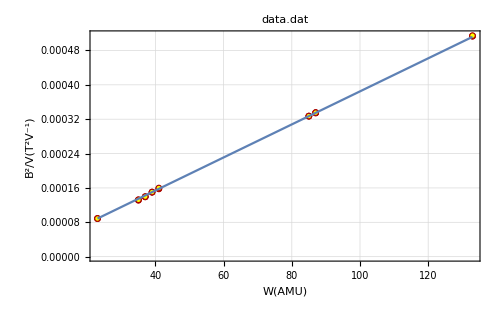
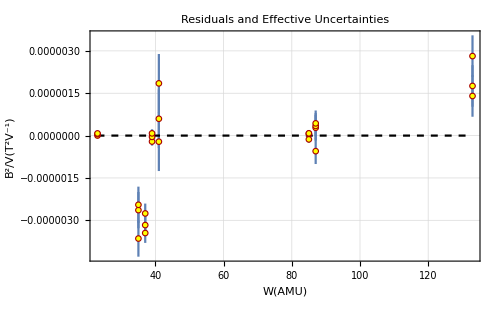
-Graphics-
-Graphics-
y(x) = a + b x
a= 
3.22344×10^-7 | b= 
3.84468×10^-6 | 
σ_a= 
3.79739×10^-8 | σ_b= 
1.0721×10^-9 | χ^2/(n-2)= 
15.1099

```mathematica
LinearDifferencePlot[FrameLabel->{"W(AMU)","B^2/V(T^2V^-1)"}]
```

```mathematica
(* We now visualize the Full Width at Half Maximum by plotting the difference between the half-maximum range and the measurement value, against W *)
QuitCurveFit
Quit[]
```

```mathematica
Needs["ErrorBarPlots`"]
```

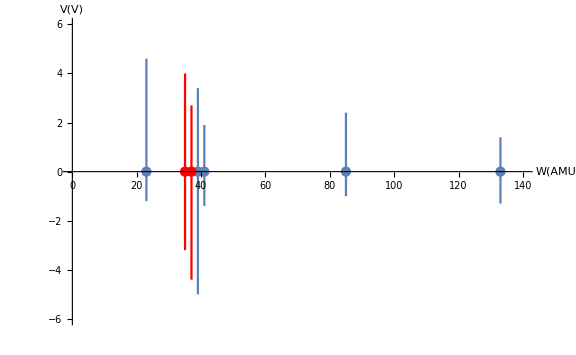

```mathematica
alkali=ErrorListPlot[{{{133,0},ErrorBar[{545.4-546.7,548.1-546.7}]},{{85,0},ErrorBar[{548.2-549.2,551.6-549.2}]},{{39,0},ErrorBar[{544.4-549.4,552.8-549.4}]},{{41,0},ErrorBar[{519.2-520.6,522.5-520.6}]},{{23,0},ErrorBar[{541.7-542.9,547.5-542.9}]}},PlotRange->{{0,140},{-6,6}},AxesLabel->{"W(AMU)","V(V)"},ImageSize->Large];
halogens=ErrorListPlot[{{{35,0},ErrorBar[{559.7-562.9,566.9-562.9}]},{{37,0},ErrorBar[{526.6-531.0,533.7-531.0}]}},PlotRange->{{0,140},{-6,6}},AxesLabel->{"W(AMU)","V(V)"},ImageSize->Large,PlotStyle->Red];
Show[alkali,halogens]
```

```mathematica
(* The halogens are shown with the red half-maximum bar *)
```

## Comments on fit and resolution

While there are no significant outliers in the data set and the fit visually looks good on the plot of the linear fit and residuals, the high reduced chi-squared of 15.1 suggests that we cannot satisfactorily use our results above alone to confirm the theory. This could be due to the large uncertainty in each measurement of B^2/V due to inaccuracies in the experimental procedure (for example, we identified the peaks by varying the accelerator and using a reading of the detector plate current to find the maximum point. This can be error-prone, particularly for broad peaks.) or to the small number of repetitions carried out for each data point.

We also notice that our fit parameter for the intercept is (3.22±0.38) ×10^-7 T^2 V^-1, a relatively strong measurement with small uncertainty. This indicates that there is an offset in our data. One possible cause could an incorrect zeroing of the Hall probe.

We nevertheless observe that the linear fit obtained suggests that the theory expressed in (9.10) is valid to within the accuracy of our experiment. We therefore use our fit parameters to estimate e/m_AMU.

We obtain a measure of the mass resolution of the spectrometer by finding the full width half maximum with respect to voltage (as stated in the pre-lab, there is a symmetry between m and V in the equations describing this system). We observe from the unexpected asymmetry in the half-maximum range as plotted above that this measurement seems quite prone to error and possibly because of this shows no particular pattern.

## Estimating e/m_AMU

We obtain from our fit parameters that the slope, say b = (3.84 ± 0.0011)×10^-6 T^2(V^-1(AMU))^-1. Then we have e/m_AMU=1/b(2/R_eff^2) =

```mathematica
ratio=1/(3.8447*10^-6)(2/0.0735^2);
NumberForm[ratio,4]
```

9.629×10^7

We can then estimate the total error in e/m_AMU as in the pre-lab: (σ_(e/m_AMU))/(e/m_AMU)=√((σ_fit/fit)^2+(2 σ_R/R)^2+2(σ_B/B))=

```mathematica
uncertainty=ratio*Sqrt[(0.0010721/3.4468)^2+(2*0.002)^2+2(0.002)^2];
ScientificForm[uncertainty,2]
```

4.7×10^5

Our estimate is therefore e/m_AMU=(9.629±0.047)×10^7 C kg^-1. Using the NIST published values for the mass of the proton and charge of the electron, we obtain e/m_AMU=

```mathematica
publishedRatio=(1.6021766208*10^-19)/(1.672621898*10^-27);
ScientificForm[publishedRatio,4]
```

9.579×10^7

This comes very close to being within the error bounds of our estimate, indicating that the experiment agrees reasonably well with the theory barring issues with the fit as described above, but by itself does not give a conclusive estimate of e/m_AMU or a conclusive assessment of the validity of the Lorentz Force law for ions.